```mathematica
Clear[m,d,ϵ,u1,v1,v2,v3,v4,v5,v6,V,etil,exp,n,g];
ϵ[m_,d_]:=m+3/(m+1)-d;
bd[m_,d_]:=(Gamma[(d -m+1)/2]Gamma[(d -m+1)/2])/(2^((2d +m-1)/2)π^((d -1)/2)Abs[Cos[((d-m+1)π)/2]]Gamma[(d -m)/2]Gamma[d-m+1]);
u1[m_,d_]:=If[m==2,1/(12 π^2),Gamma[(m+4)/(2(m+1))]/(2^(m-1)π^((m-2)/2)(4π)^(3/(2(m+1)))bd[m,d]^((2-m)/2)(m+1)Gamma[m/2]Gamma[(2-m)/(2(m+1))])1/(Gamma[(2m+5)/(2(m+1))]Sin[(m+1)/3 π])];
v1[m_,d_]:=Gamma[(m+1)/3]/bd[m,d]^((2-m)/2);
v2[m_,d_]:=2^(2-2d+m/2)/(π^(d/2)Gamma[(d-m)/2]);(* I had earlier 2^(2+2d-m/2)/(π^(d/2) Gamma[(d-m)/2]) => typo and error *)
v3[m_,d_]:= (2 EulerGamma)/(bd[m,d]^((2-m)/2)(2π)^(3/(5-m)+m-2)Gamma[m/2]Gamma[3/(2(m+1))]π);
v4[m_,d_]:= (6 EulerGamma)/(bd[m,d]^((2-m)/2)(2π)^(3/(5-m)+m-2)Gamma[m/2]Gamma[3/(2(m+1))]π(m+1))-2/3;
v5[m_,d_]:= (2^(5-2d +m/2) EulerGamma Gamma[(m+1)/3])/(bd[m,d]^((2-m)/2)(π)^(d/2)Gamma[(d-m)/2]);
v6[m_,d_]:=-(2^(5-2d+m/2) EulerGamma Gamma[(m+1)/3])/(bd[m,d]^((2-m)/2)(π)^(d/2)Gamma[(d-m)/2]);
g[m_,d_]:=1-(2-m)/((m+1)ϵ[m,d]);
etil[m_,d_,n_]:=If[m+3/(m+1)>=d,(n ϵ[m,d])/u1[m,d],0];(* ẽ is zero at & above dc *)


(* -Graphics- -Graphics-*)
eqn[m_,d_,V_,n_](* = - δVt/δl*):=-V ( ϵ[m,d]-(2-m)/(m+1))+v2[m,d] V^2+((7-m^2) v1[m,d])/(6 (1+m) n)etil[m,d,n]-(((5-m^2-2m)(3v5[m,d]-v6[m,d]))/(m+1)+(m-1)v3[m,d]-2(m+1)(u1[m,d]+v4[m,d]))(etil[m,d,n] V)/(6n);

eqn1[m_,d_,V_,et_,n_]:=-V (ϵ[m,d]-(2-m)/(m+1)) +v2[m,d] V^2+((7-m^2) v1[m,d])/(6 (1+m) n)et-(((5-m^2-2m)(3v5[m,d]-v6[m,d]))/(m+1)+(m-1)v3[m,d]-2(m+1)(u1[m,d]+v4[m,d]))et/(6n) UnitStep[ϵ[m,d]];
```

```mathematica
etil[1,5/2,2]
```

0

```mathematica
Clear[d,m,V,r,sol];
sol[d_,m_]=SolveValues[eqn1[m,d,V,etilde=0,n]==0,V]//FullSimplify
```

{0,-2^(-2+2 d-m/2) (-1+d-m) π^(d/2) Gamma[(d-m)/2]}

```mathematica
(* ColorFunction->Function[{x,y,z},Hue[z]] *)
```

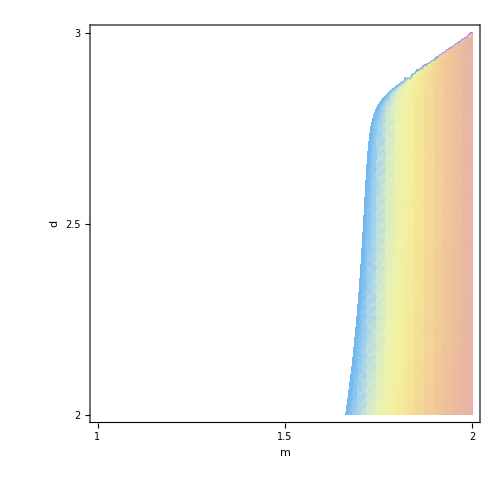

```mathematica
Clear[ans];
ans[d_,m_]:=NSolveValues[eqn[m,d,Vt,2]==0,Vt];root1=Quiet[DensityPlot[(**)Chop[ans[d,m][[1]]](***) ,{m,1,2},{d,2,3},BaseStyle->Directive[Black,Bold,22,FontFamily->"Times"],Frame->True,FrameLabel->{"m","d"},FrameTicks->{{{2,2.5,3},None},{{1,1.5,2},None}},ColorFunction->"Pastel",PerformanceGoal->"Quality",(*********)ColorFunctionScaling->False,RegionFunction->Function[{x,y,z},-1<Chop[Re[z]]<1],PlotPoints->40,ImagePadding->{{80, 40}, {Automatic,Automatic}},FrameStyle->Directive[Black,Bold,22],FrameTicksStyle->Directive[Darker[Gray],Bold,18],ImageSize->500,PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[Bold,FontSize->18,FontFamily->"Times"]],Below]]]
```

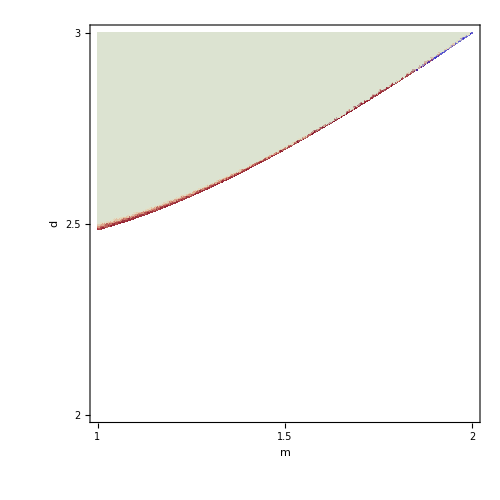

```mathematica
root2=Quiet[DensityPlot[(**)Chop[ans[d,m][[2]]](**),{m,1,2},{d,2,3},BaseStyle->Directive[Black,Bold,22,FontFamily->"Times"],Frame->True,FrameLabel->{"m","d"},FrameTicks->{{{2,2.5,3},None},{{1,1.5,2 },None}},ColorFunction->(ColorData[{"ThermometerColors","Reverse"}][Rescale[Re[#],{-1,1}]]&),(************)ColorFunctionScaling->False,PerformanceGoal->"Quality",PlotPoints->40,RegionFunction->Function[{x,y,z},-1<Re[z]<1],ImagePadding->{{80, 40}, {Automatic,Automatic}},FrameStyle->Directive[Black,Bold,22],FrameTicksStyle->Directive[Darker[Gray],Bold,18],ImageSize->500,PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[Bold,FontSize->18,FontFamily->"Times"]],Below]]]
```

```mathematica
p=Plot[{d=m+1,d=m+3/(m+1)},{m,1,2},PlotStyle->{Directive[Darker[Red],Dashed,Thick],Directive[Black,Dashed,Thick]},Frame->True,Axes->False];
r1=Show[root1,p];
r2=Show[root2,p];
SetDirectory[NotebookDirectory[]];
Export["root1.jpg",Rasterize[r1,ImageResolution-> 500],ImageSize->500];
Export["root2.jpg",Rasterize[r2,ImageResolution-> 500],ImageSize->500];
```

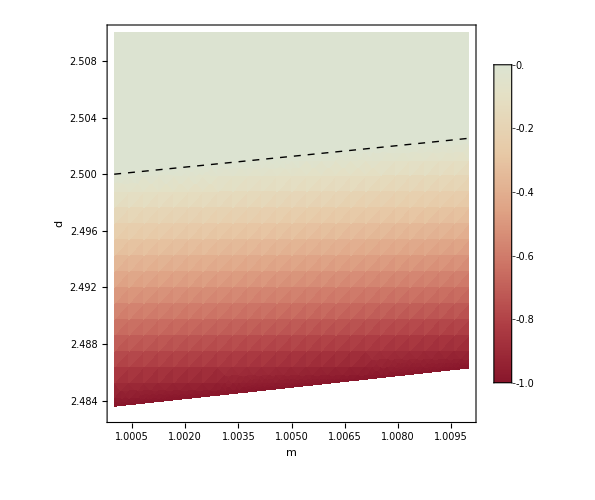

```mathematica
Clear[ans];ans[d_,m_]:=NSolveValues[eqn[m,d,Vt,2]==0,Vt];
root2=DensityPlot[Chop[ans[d,m][[2]]],{m,1,1.01},{d,2.483,2.51},BaseStyle->Directive[Black,Bold,22,FontFamily->"Times"],Frame->True,FrameLabel->{"m","d"},ColorFunction->(ColorData[{"ThermometerColors","Reverse"}][Rescale[Re[#],{-1,1}]]&),ColorFunctionScaling->False,PerformanceGoal->"Quality",PlotPoints->25,RegionFunction->Function[{x,y,z},-1<Chop[Re[z]]<1],ImagePadding->{{80, 40}, {Automatic,Automatic}},FrameStyle->Directive[Black,Bold,22],FrameTicksStyle->Directive[Darker[Gray],Bold,18],ImageSize->500,PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[Bold,FontSize->18,FontFamily->"Times"]],Right]];
p=Plot[{d=m+1,d=m+3/(m+1)},{m,1,1.01},PlotStyle->{Directive[Darker[Red],Dashed,Thick],Directive[Black,Dashed,Thick]},Frame->True,Axes->False];
r2=Show[root2,p]

SetDirectory[NotebookDirectory[]];
Export["root2_enlarged.jpg",Rasterize[r2,ImageResolution-> 500],ImageSize->500];
```

```mathematica
Export["root2_enlarged.jpg",Rasterize[r2,ImageResolution-> 500],ImageSize->500]
```

root2_enlarged.jpg